(v≠0&&s==0)||(C[1]∈Integers&&d v≠0&&s+v≠0&&s==(-d v+ProductLog[C[1],d ⅇ^(d v) v])/d)

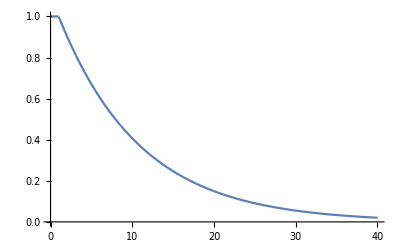

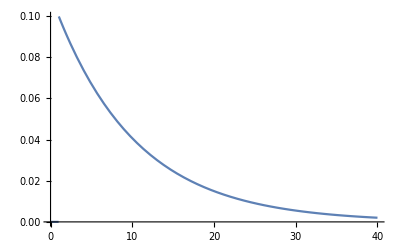

(0.1 ⅇ^(-a-ⅈ b))/(0.1+a+ⅈ b)

a+ⅈ b

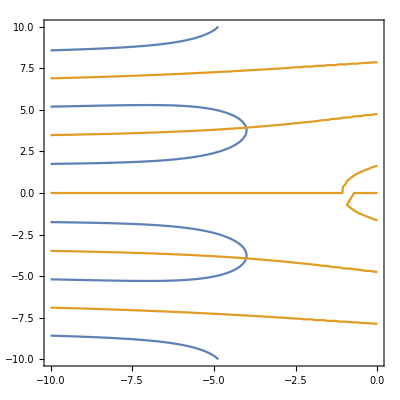

-Graphics3D-

-Graphics3D-

```mathematica
τ=.
d=.
ρ=.
v=.
PL=.

param={d->1, v->0.1};


ρ[t_]=HeavisideTheta[t-d]*v;

Pisi[t_]=v*HeavisideTheta[t-d]*Exp[-v*(t-d)];

S[t_]=HeavisideTheta[d-t ]+HeavisideTheta[t-d]*Exp[-v*(t-d)];

PL[s_]=v/(v+s)*Exp[-s*d];

Reduce[PL[s]==1,s]




Splot=S[t]/.param;
Pplot=Pisi[t]/.param;

Plot[Splot,{t,0,40}]/.param
Plot[Pplot,{t,0,40}]/.param

PLplot=PL[ll]/.param



ll=a+I*b

ContourPlot[{Re[PLplot]==1,Im[PLplot]==0},{a,-10,0},{b,-10,10}]

Plot3D[{Re[(PLplot)]},{a,-1,0},{b,-1,1}]
Plot3D[{Im[(PLplot)]},{a,-1,0},{b,-1,1}]
```

```mathematica
InverseFourier[v*(1+2*v^2/w^2*(1-Cos[w*d])+2*v/w*Sin[w*d])^(-1),w,t]
```

InverseFourier::nonopt: Options expected (instead of t) beyond position 2 in InverseFourier[v/(1+(2 v^2 (1-Cos[«1»]))/w^2+(2 v Sin[d w])/w),w,t]. An option must be a rule or a list of rules.

InverseFourier::nonopt: Options expected (instead of t) beyond position 2 in InverseFourier[0.1/(1+(0.02 (1-Cos[«1»]))/w^2+(0.2 Sin[w])/w),w,t]. An option must be a rule or a list of rules.

InverseFourier[0.1/(1+(0.02 (1-Cos[w]))/w^2+(0.2 Sin[w])/w),w,t]

Set::write: Tag Times in (2 ⅇ^(-2 (100 (-1+ⅇ^Times[«2»])+t)) (1-ⅇ^(-t/100)))[τ_] is Protected.